```mathematica
dt =0.1;
k = 2;
m = 0.5;
{x0,v0} = {-1,-2};
{xp0,vp0}= {-2,4};

hist2= {};
Do[{{x,v} = {x0,v0} + dt/2({v0, -k/m x0} + {v0 + dt vp0, -k/m(x0 +dt xp0)}),
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -k/m x0},AppendTo[hist2, {x,v}]},{i ,1,6}]
```

```mathematica
hist2
```

{{-1.18,-1.56},{-1.3124,-1.0568},{-1.39183,-0.510704},{-1.41507,0.0562429},{-1.38114,0.621144},{-1.2914,1.16118}}

```mathematica
dt =0.01;
k = 2;
m = 0.5;
{x0,v0} = {-1,-2};
{xp0,vp0}= {-2,4};

hist2= {};
Do[{{x,v} = {x0,v0} + dt/2({v0, -k/m x0} + {v0 + dt vp0, -k/m(x0 +dt xp0)}),
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -k/m x0},AppendTo[hist2, {x,v}]},{i ,1,500}]
```

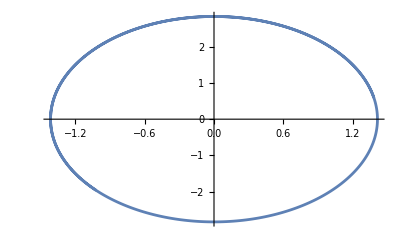

```mathematica
plot1 = ListPlot[hist2,Joined->True]
```

```mathematica
dt =0.01;
k = 2;
m = 0.5;
{x0,v0} = {-1,-2};
{xp0,vp0}= {-2,4};

hist2= {};
Do[{{x,v} = {x0,v0} + dt/2({v0, -k/m x0} + {v0 + dt vp0, -k/m(x0 +dt xp0)}),
{x0,v0} = {x,v},
{xp0, vp0} = {v0, -k/m x0},AppendTo[hist2, {x,v}]},{i ,1,5000}]
```

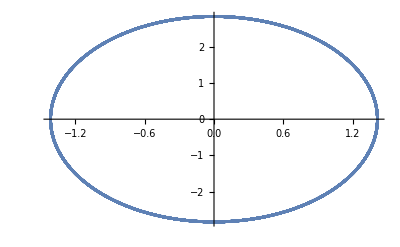

```mathematica
plot2 = ListPlot[hist2,Joined->True]
```

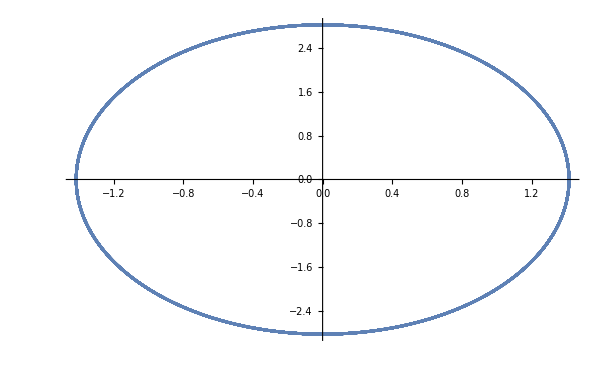

```mathematica
Show[{plot1,plot2}]
```